## Init data

```mathematica
(*xi≥0*)
InitF:=2*x1-4*x2+3;

(*n<m*)
InitLimit1:=3*x1≥8*x2;
InitLimit2:=2*x1+3*x2≤6;
InitLimit3:=x1-x2≤4;
InitLimit4:=-2*x1+x2≤2;

export[name_, data_]:=Export["ММиАвАП\\lab5\\"<>name<>".png", data]
```

## Geometric

### Limits

```mathematica
L1:=3*x1-x3==8*x2;
L2:=2*x1+3*x2+x4==6;
L3:=x1-x2+x5==4;
L4:=-2*x1+x2+x6==2;
```

### Used functions

```mathematica
FormInequalities:=Module[{a,b,c,d},
a=(x3/.Solve[L1,x3])[[1]]≥0;
b=(x4/.Solve[L2,x4])[[1]]≥0;
c=(x5/.Solve[L3,x5])[[1]]≥0;
d=(x6/.Solve[L4,x6])[[1]]≥0;
Return[{a,b,c,d}];
];

FormInequalitiesInv:=Module[{a,b,c,d},
a=(x3/.Solve[L1,x3])[[1]]≤0;
b=(x4/.Solve[L2,x4])[[1]]≤0;
c=(x5/.Solve[L3,x5])[[1]]≤0;
d=(x6/.Solve[L4,x6])[[1]]≤0;
Return[{a,b,c,d}];
];

FormArea:=Module[{inEqs=FormInequalitiesInv, plot},
plot=RegionPlot[{inEqs},{x1,0,10},{x2,0,5},PlotLegends->{FormInequalities}, AxesLabel->Automatic, AspectRatio->Automatic];
Return[plot];
];

FindMinMax:=Module[{min, max, inEqs=FormInequalities},
min = FindMinimum[{2*x1-4*x2+3,inEqs[[1]]&&inEqs[[2]]&&inEqs[[3]]&&inEqs[[4]]&& x1≥0&&x2≥0},{x1,x2}];
max = FindMaximum[{2*x1-4*x2+3,inEqs[[1]]&&inEqs[[2]]&&inEqs[[3]]&&inEqs[[4]]&& x1≥0&&x2≥0},{x1,x2}];
Return[{min,max}];
];

ReduceIneqs:=Module[{res, inEqs=FormInequalities},
res=Reduce[inEqs[[1]]&&inEqs[[2]]&&inEqs[[3]]&&inEqs[[4]]&& x1≥0&&x2≥0,{x1,x2}];
Return[res];
];
```

### Using plots

x1==0&&x2==00<x1≤48/25&&0≤x2≤(3 x1)/848/25<x1<3&&0≤x2≤1/3 (6-2 x1)x1==3&&x2==0

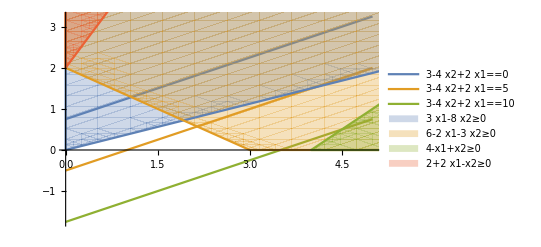

```mathematica
Row[{ReduceIneqs[[1]],ReduceIneqs[[2]],ReduceIneqs[[3]],ReduceIneqs[[4]]},"\n"]
Module[{a,b,c,d,min,max},
OrigF[y_]:=x2/.Solve[InitF==y,x2];
Show[{Plot[{OrigF[0], OrigF[5], OrigF[10]},{x1,0,5},PlotLegends->{InitF==0,InitF==5,InitF==10}, PlotStyle->Thick],FormArea}]
]
```

```mathematica
Row[{"Fmin",Row[{Assuming[x1==0&&x2==0,Refine[InitF]],"(x1→0, x2→0)"},","]},"="]
```

==Fmin,,3(x1→0, x2→0)

### Built-in functionality (just for test)

```mathematica
FindMinMax
```

{{3.,{x1→0.,x2→0.}},{9.,{x1→3.,x2→0.}}}

## Simplex

### Limits

```mathematica
Fs:=3-(-2*x1+4*x2);
L1s:=x3==0-(-3*x1+8*x2);
L2s:=x4==6-(2*x1+3*x2);
L3s:=x5==4-(1*x1-1*x2);
L4s:=x6==2-(-2*x1+1*x2);
```

т.к. свободные члены во всех ограничения больше 0, то ограничения совместны

#### min

т.к. условие оптимальности не выполняется (все коэффициенты при свободных  переменных разных знаков), необходимо выбрать новую базисную переменную
в соответствии с правилом выбора свободной переменной в базис переводим переменную x2
в соответствии с правилом выбора базисной переменной в свободные переменные переводим x3

```mathematica
FsMin:=3-(-x1/2-x3/2);
L1sMin:=x2==0-(-3*x1/8+x3/8);
L2sMin:=x4==6-(2*x1+3*x2);
L3sMin:=x5==4-(1*x1-1*x2);
L4sMin:=x6==2-(-2*x1+1*x2);
```

т.к. теперь коэффициенты при всех свободных переменных целевой функции отрицательны, выполняется условие оптимального решения
и целевая функция будет иметь минимальное значение

```mathematica
Row[{"Fmin",Row[{Assuming[x1==0&&x3==0,Refine[FsMin]],"(x1→0, x3→0)"},","]},"="]
```

==Fmin,,3(x1→0, x3→0)

#### max

Все коэффициенты при свободных  переменных (x1, x2) разных знакову, поэтому условие оптимальности не выполняется.
Необходимо выбрать новую базисную переменную. В соответствии с правилом выбора свободной переменной в базис переводим переменную x1.
В соответствии с правилом выбора базисной переменной в свободные переменные переводим x3.

```mathematica
FsMax:=3-(-4*x2/3-2*x3/3);
L1sMax:=x1==0-(8x2/3+x3/3);
L2sMax:=x4==6-(2*x1+3*x2);
L3sMax:=x5==4-(1*x1-1*x2);
L4sMax:=x6==2-(-2*x1+1*x2);
```

Все коэффициенты при свободных  переменных (x2, x3) отрицательные, что говорит о выполнении признака оптимальности для поиска минимума
Поэтому в свободные переменные переводим x4.

```mathematica
FsMax:=9-(7x2+x4);
L1sMax:=x3==0-(-3*x1+8*x2);
L2sMax:=x1==3-(3*x2/2+x4/2);
L3sMax:=x5==4-(1*x1-1*x2);
L4sMax:=x6==2-(-2*x1+1*x2);
```

Теперь коэффициенты при всех свободных переменных (x2, x4) целевой функции отрицательны, выполняется условие оптимального решения
и целевая функция будет иметь минимальное значение

```mathematica
Row[{"Fmax",Row[{Assuming[x2==0&&x4==0,Refine[FsMax]],"(x2→0, x4→0)"},","]},"="]
```

==Fmax,,9(x2→0, x4→0)